Experimental data

```mathematica
(*data consists of pairs (Δρ, Rg), where Δρ is the total contrast (obtained from Mulch), and of total contrast and Rg is the radius of gyration (from GNOME) *)
```

```mathematica
data={{2.980,28.7},{2.420,28.3},{1.860,28.9},{0.740,24.2}(*,{-0.940,15}*),{-1.500,23.2},{-2.060,24.4},{-2.620,25.1}}
```

{{2.98,28.7},{2.42,28.3},{1.86,28.9},{0.74,24.2},{-1.5,23.2},{-2.06,24.4},{-2.62,25.1}}

```mathematica
(*Rg errors*)
```

```mathematica
errors={5.7,11.3,11.6,29,(*240,*)9.3,14.6,15.1}
```

{5.7,11.3,11.6,29,9.3,14.6,15.1}

```mathematica
(*extracting the contrast and calculating its inverse*)
```

```mathematica
inversecontrast=data⟦;;,1⟧^-1
```

{0.33557,0.413223,0.537634,1.35135,-0.666667,-0.485437,-0.381679}

```mathematica
squaredRg=data⟦;;,2⟧^2
```

{823.69,800.89,835.21,585.64,538.24,595.36,630.01}

```mathematica
(*including errors in Rg*)
finalRg=Table[Around[squaredRg⟦i⟧,errors⟦i⟧],{i,1,Length[errors]}]
```

{824.6.,801.11.,835.12.,586.29.,538.9.,595.15.,630.15.}

```mathematica
(*----*)
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
(*combining the results and sorting the points in increasing order of the inversecontrast*)
```

```mathematica
pointswitherrors=Sort[Partition[Riffle[inversecontrast,squaredRg],2],#1⟦1⟧<#2⟦1⟧&]
```

{{-0.666667,538.24},{-0.485437,595.36},{-0.381679,630.01},{0.33557,823.69},{0.413223,800.89},{0.537634,835.21},{1.35135,585.64}}

```mathematica
?ErrorListPlot
```

```mathematica
pts={{pointswitherrors⟦1⟧,ErrorBar[9.3]},{pointswitherrors⟦2⟧,ErrorBar[14.6]},{pointswitherrors⟦3⟧,ErrorBar[15.1]},{pointswitherrors⟦4⟧,ErrorBar[5.7]},{pointswitherrors⟦5⟧,ErrorBar[11.3]},{pointswitherrors⟦6⟧,ErrorBar[11.6]},{pointswitherrors⟦7⟧,ErrorBar[29]}}
```

{{{-0.666667,538.24},ErrorBar[9.3]},{{-0.485437,595.36},ErrorBar[14.6]},{{-0.381679,630.01},ErrorBar[15.1]},{{0.33557,823.69},ErrorBar[5.7]},{{0.413223,800.89},ErrorBar[11.3]},{{0.537634,835.21},ErrorBar[11.6]},{{1.35135,585.64},ErrorBar[29]}}

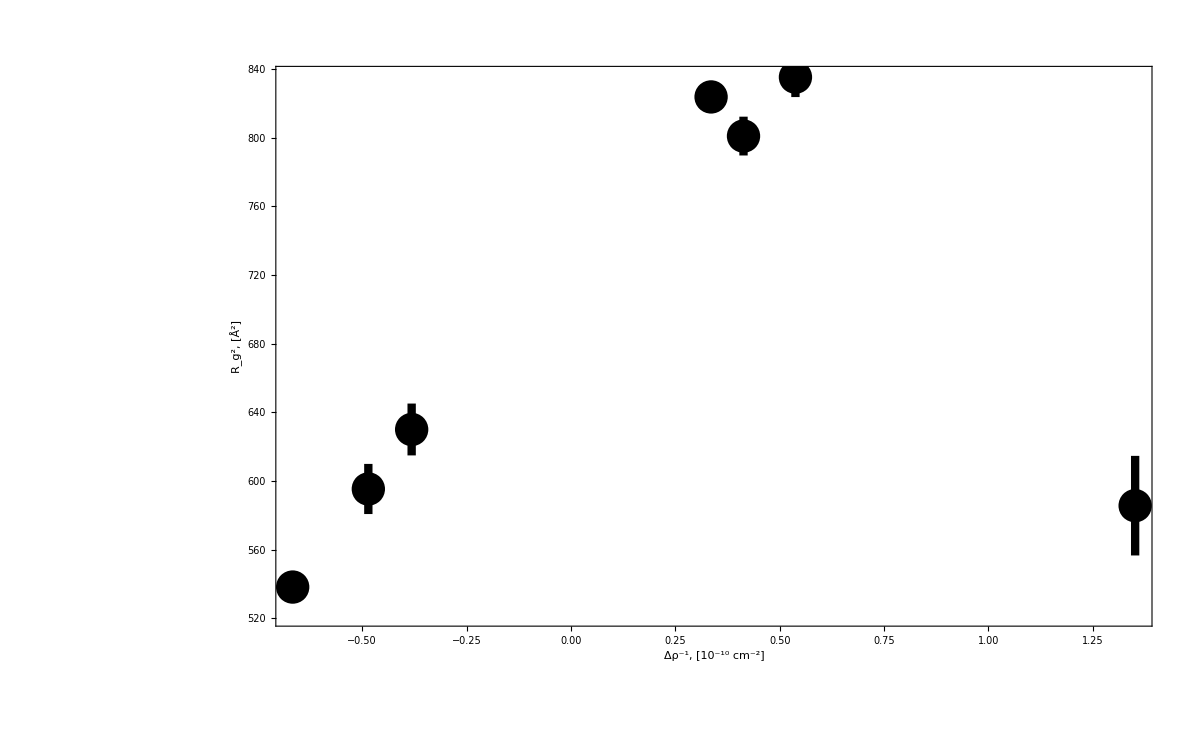

```mathematica
pointswitherrors=ErrorListPlot[pts,PlotStyle->{Black,PointSize[0.02],Thickness[.005]},Epilog->Inset[Style["i",56,Bold],{-1.24,857}],Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Directive[Black,44,Thick],FrameLabel->{"Δρ^-1, [10^-10 cm^-2]","R_g^2, [Å^2]"},PlotRangeClipping->False,ImageSize->1200]
```

```mathematica
(*Fitting data*)
```

```mathematica
pointswithouterrors=Sort[Partition[Riffle[inversecontrast,squaredRg],2],#1⟦1⟧<#2⟦1⟧&]
```

{{-0.666667,538.24},{-0.485437,595.36},{-0.381679,630.01},{0.33557,823.69},{0.413223,800.89},{0.537634,835.21},{1.35135,585.64}}

```mathematica
nlm=NonlinearModelFit[pointswithouterrors,a+b x+c x^2,{a,b,c},x,Weights->1/errors]
```

FittedModel[767.951+202.567 x-245.445 x^2]

```mathematica
nlm[{"ParameterTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 767.951 | 13.2017 | 58.1706 | 5.22978×10^-7
b | 202.567 | 16.4663 | 12.3019 | 0.000250823
c | -245.445 | 22.1549 | -11.0786 | 0.000377555}

```mathematica
(**)
```

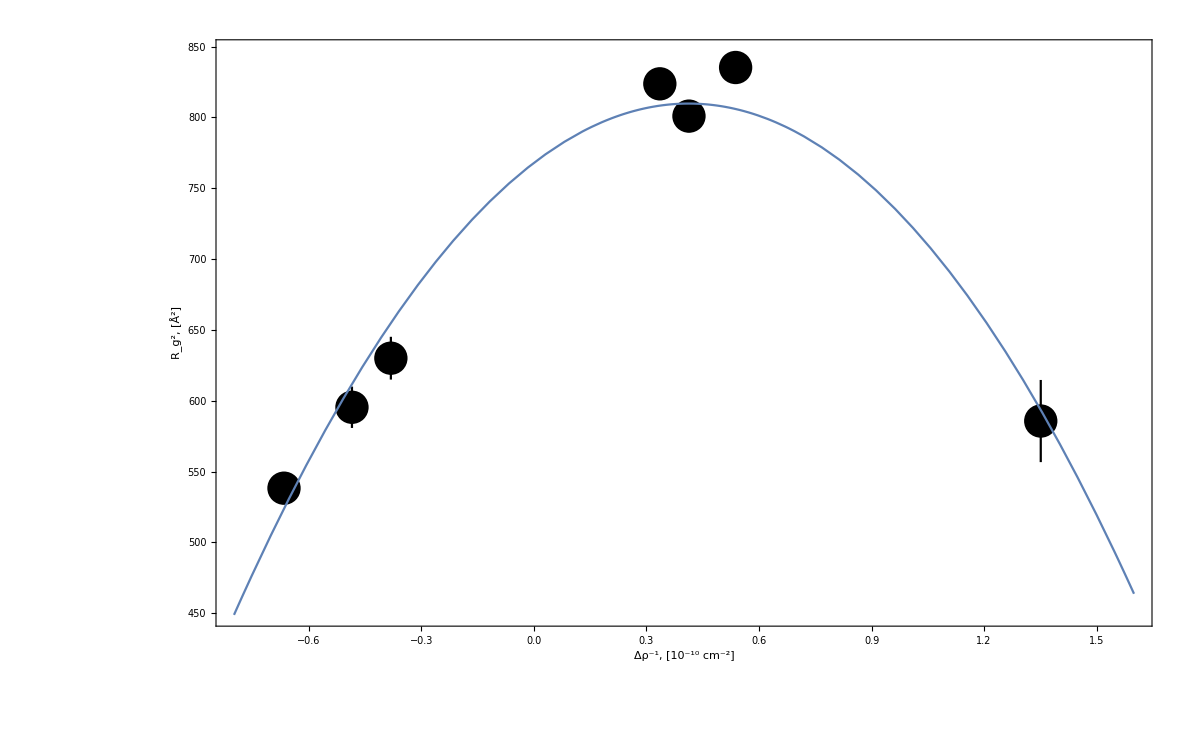

```mathematica
Show[pointswitherrors,Plot[nlm[x],{x,-0.8,1.6}],PlotRange->All]
```

Alpha-shape data

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 772.91 | 14.4786 | 53.3829 | 7.37099×10^-7
b | 191.135 | 21.8555 | 8.74539 | 0.000942096
c | -262.195 | 25.4508 | -10.302 | 0.000500796}

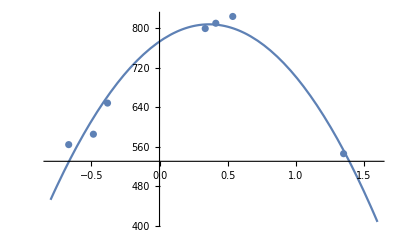

```mathematica
alphadata={{2.980,28.27},{2.420,28.46},{1.860,28.7},{0.740,23.36},(*{-0.940,20.65},*){-1.500,23.75},{-2.060,24.19},{-2.620,25.46}};
alphainversecontrast=alphadata⟦;;,1⟧^-1;
alphasquaredRg=alphadata⟦;;,2⟧^2;
alphapoints=Sort[Partition[Riffle[alphainversecontrast,alphasquaredRg],2],#1⟦1⟧<#2⟦1⟧&];
alphanlm=NonlinearModelFit[alphapoints,a+b x+c x^2,{a,b,c},x];
alphanlm[{"ParameterTable"}]
Show[ListPlot[alphapoints],Plot[alphanlm[x],{x,-0.8,1.6}],PlotRange->All]
```

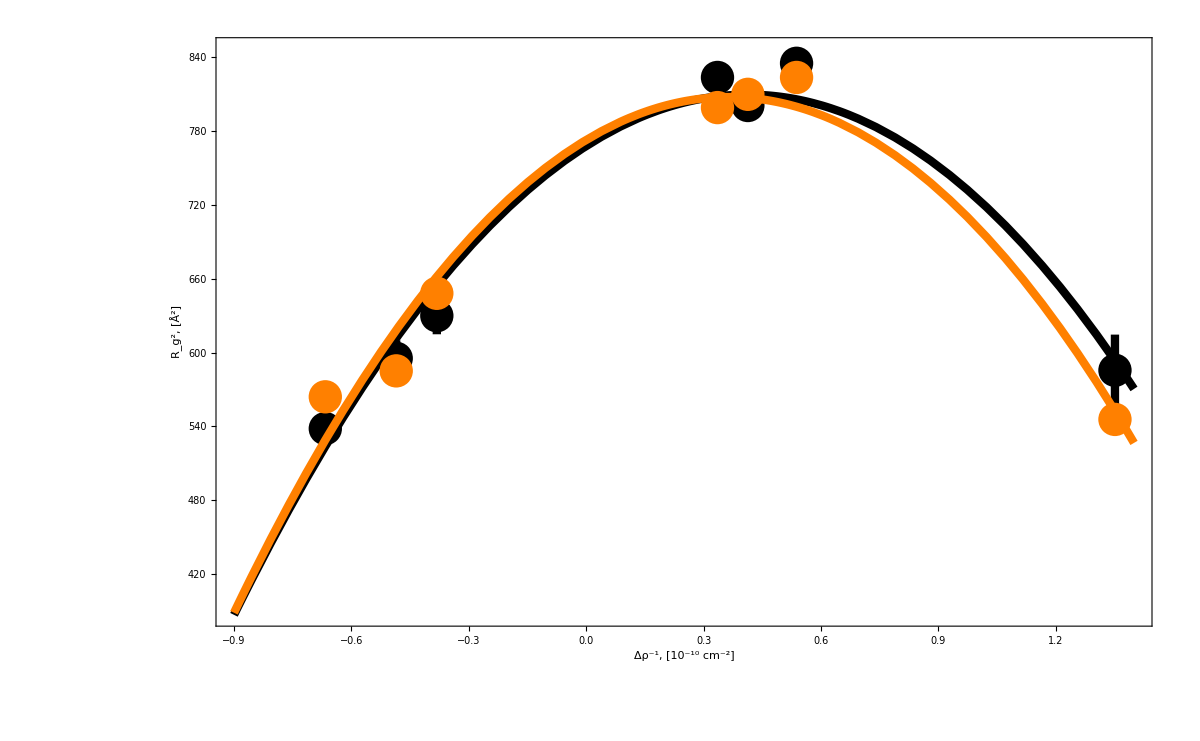

```mathematica
finalplot=Show[pointswitherrors,Plot[nlm[x],{x,-0.9,1.4},PlotStyle->{Black,Thickness[0.005]}],ListPlot[alphapoints,PlotStyle->{Orange,PointSize[0.02]}],Plot[alphanlm[x],{x,-0.9,1.4},PlotStyle->{Orange,Thickness[0.005]}],PlotRange->All]
```

```mathematica
Export["fig4i.png",finalplot]
```

fig4i.png